```mathematica
(* Sets the Base directory, changing which files are easiest to acces. *)
dropBoxOn=FileNameJoin[{"Dropbox","00School","research"}];
labComp=FileNameJoin[{"C:","Users","karl",dropBoxOn}];(* Lab computer is Windows, so needs "C:" at beginning"  *)
homeComp=FileNameJoin[{"/","home","karl",dropBoxOn}]; (* Home coputer is Linux, so needs "/" at beginning *)
(* The folder that contains the different data runs to analyze, this folder contains subfolders with 
individual runs.*)
dataFolder=FileNameJoin[{homeComp}]
SetDirectory[dataFolder];
(* Make a list of directories to easily select the folder you would like to work with.*)
directories=Select[FileNames["*","",1],DirectoryQ];
For[i=1,i<=Length[directories],i++,
Print[i -> directories[[i]]];]
```

/home/karl/Dropbox/00School/research

1→3_15_17_AimingFor5e12

2→4-18-17

3→4-22-17

4→data

5→Data Before 4-1-17

6→firstRun2017

7→labBook

8→legacy

9→machineShopOrders

10→mathematicaCode

11→mathematicaRb

12→operationManuals

13→papers

14→polarization_4-18-17

15→polarization_4-4-17

16→polarization_4-6-17

17→probeLaserPower

18→pumpLaserFindingCircular_3-29_17

19→RbControlPiPrograms

20→rbsim

21→requisitions

22→wavemeterNoRb

23→wavemeterReliability_3-30-17

24→wmReliability_4-7-17

```mathematica
(* set rootFolder to the folder name containing the desired Files *)
rootFolder=FileNameJoin[{dataFolder,directories[[3]]}];
SetDirectory[rootFolder];
(* Obtain the filenames of the rotation data and print them out.*)
scanFiles=FileNames["FDayScan"~~RegularExpression[".{25,25}"]~~"Analysis.dat"];
For[i=1,i<=Length[scanFiles],i++,
Print[i -> scanFiles[[i]]];]

(*Import the faraday rotation data*)
rotationAnalysisDataFile=Import[FileNameJoin[{rootFolder,scanFiles[[3]]}],"tsv"];
```

1→FDayScan2017-04-22_185001RotationAnalysis.dat

2→FDayScan2017-04-22_185501RotationAnalysis.dat

3→FDayScan2017-04-22_190001RotationAnalysis.dat

4→FDayScan2017-04-22_190501RotationAnalysis.dat

5→FDayScan2017-04-22_191001RotationAnalysis.dat

6→FDayScan2017-04-22_191501RotationAnalysis.dat

7→FDayScan2017-04-22_192001RotationAnalysis.dat

8→FDayScan2017-04-22_192501RotationAnalysis.dat

9→FDayScan2017-04-22_193001RotationAnalysis.dat

10→FDayScan2017-04-22_193314RotationAnalysis.dat

11→FDayScan2017-04-22_193346RotationAnalysis.dat

12→FDayScan2017-04-22_193459RotationAnalysis.dat

13→FDayScan2017-04-22_194043RotationAnalysis.dat

14→FDayScan2017-04-22_195505RotationAnalysis.dat

15→FDayScan2017-04-22_200102RotationAnalysis.dat

16→FDayScan2017-04-22_200607RotationAnalysis.dat

17→FDayScan2017-04-22_201134RotationAnalysis.dat

18→FDayScan2017-04-22_201631RotationAnalysis.dat

19→FDayScan2017-04-22_202122RotationAnalysis.dat

20→FDayScan2017-04-22_203001RotationAnalysis.dat

21→FDayScan2017-04-22_204001RotationAnalysis.dat

22→FDayScan2017-04-22_205001RotationAnalysis.dat

23→FDayScan2017-04-22_210001RotationAnalysis.dat

24→FDayScan2017-04-22_211001RotationAnalysis.dat

25→FDayScan2017-04-22_212001RotationAnalysis.dat

26→FDayScan2017-04-22_213501RotationAnalysis.dat

27→FDayScan2017-04-22_214501RotationAnalysis.dat

28→FDayScan2017-04-22_215501RotationAnalysis.dat

29→FDayScan2017-04-22_220502RotationAnalysis.dat

30→FDayScan2017-04-22_221501RotationAnalysis.dat

31→FDayScan2017-04-22_224433RotationAnalysis.dat

32→FDayScan2017-04-22_224930RotationAnalysis.dat

33→FDayScan2017-04-22_230006RotationAnalysis.dat

34→FDayScan2017-04-22_233140RotationAnalysis.dat

35→FDayScan2017-04-22_234019RotationAnalysis.dat

36→FDayScan2017-04-22_234854RotationAnalysis.dat

37→FDayScan2017-04-22_235949RotationAnalysis.dat

38→FDayScan2017-04-23_000130RotationAnalysis.dat

39→FDayScan2017-04-23_000201RotationAnalysis.dat

40→FDayScan2017-04-23_002022RotationAnalysis.dat

41→FDayScan2017-04-23_002053RotationAnalysis.dat

42→FDayScan2017-04-23_002124RotationAnalysis.dat

43→FDayScan2017-04-23_002232RotationAnalysis.dat

44→FDayScan2017-04-23_003214RotationAnalysis.dat

45→FDayScan2017-04-23_004019RotationAnalysis.dat

46→FDayScan2017-04-23_004823RotationAnalysis.dat

47→FDayScan2017-04-23_005847RotationAnalysis.dat

48→FDayScan2017-04-23_010331RotationAnalysis.dat

49→FDayScan2017-04-23_010415RotationAnalysis.dat

50→FDayScan2017-04-23_020029RotationAnalysis.dat

51→FDayScan2017-04-23_020501RotationAnalysis.dat

52→FDayScan2017-04-23_021501RotationAnalysis.dat

53→FDayScan2017-04-23_022501RotationAnalysis.dat

54→FDayScan2017-04-23_025120RotationAnalysis.dat

55→FDayScan2017-04-23_030229RotationAnalysis.dat

56→FDayScan2017-04-23_030416RotationAnalysis.dat

57→FDayScan2017-04-23_030445RotationAnalysis.dat

58→FDayScan2017-04-23_030729RotationAnalysis.dat

59→FDayScan2017-04-23_031534RotationAnalysis.dat

60→FDayScan2017-04-23_032338RotationAnalysis.dat

61→FDayScan2017-04-23_033307RotationAnalysis.dat

62→FDayScan2017-04-23_034110RotationAnalysis.dat

63→FDayScan2017-04-23_034914RotationAnalysis.dat

64→FDayScan2017-04-23_035826RotationAnalysis.dat

65→FDayScan2017-04-23_040145RotationAnalysis.dat

66→FDayScan2017-04-23_040500RotationAnalysis.dat

67→FDayScan2017-04-23_040922RotationAnalysis.dat

68→FDayScan2017-04-23_041243RotationAnalysis.dat

69→FDayScan2017-04-23_041605RotationAnalysis.dat

70→FDayScan2017-04-23_042059RotationAnalysis.dat

71→FDayScan2017-04-23_042416RotationAnalysis.dat

72→FDayScan2017-04-23_042735RotationAnalysis.dat

73→FDayScan2017-04-23_043117RotationAnalysis.dat

74→FDayScan2017-04-23_043745RotationAnalysis.dat

75→FDayScan2017-04-23_044417RotationAnalysis.dat

65.3

64.5

200

500

800

{{-3.53303,-80.3874},{-4.52917,57.2987},{-5.71504,46.6508},{-6.80604,40.345},{-8.1342,36.7201},{-9.36748,34.3551},{-10.6482,32.7434},{-11.8815,31.6676},{-13.1621,30.7014},{-14.4903,30.0649},{-16.0318,29.5929},{-17.4311,29.2383},{-19.0437,29.0121},{-20.7038,28.4261},{-22.4113,28.5372},{-24.2137,28.1886},{-25.9212,25.1627},{-27.6286,28.0034},{-29.4309,28.0077},{-31.1383,27.8408}}

200

600

950

{{-6.71117,46.9223},{-7.23295,42.5356},{-8.32393,38.9077},{-9.46235,36.4242},{-10.6838,34.7227},{-11.834,33.4087},{-13.1147,32.5829},{-14.348,31.9825},{-15.6761,31.1936},{-16.9567,30.7454},{-18.3323,30.3406},{-19.7552,30.0953},{-21.19,29.6517},{-22.601,29.5342},{-24.0714,29.1021},{-25.4943,29.0817},{-27.012,29.0975},{-28.5298,28.726},{-30.0475,28.4503},{-31.5652,28.3891}}

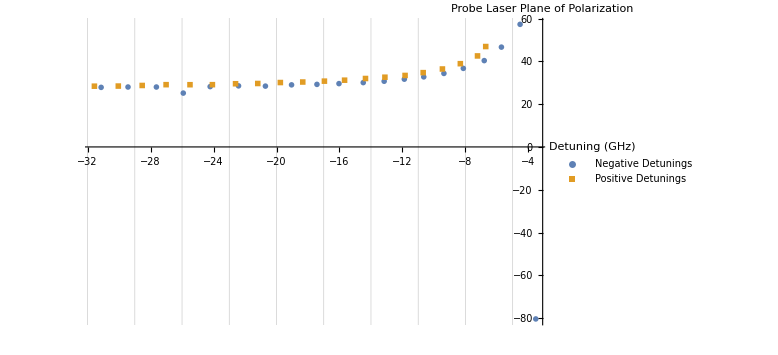

55.7622

1.91605

0.034361

```mathematica
(* Define important constants of data processing *)
fileNumber=34;
rotationAnalysisData=Import[FileNameJoin[{rootFolder,scanFiles[[fileNumber]]}],"tsv"];
rotAnalDataStartRow=16; (* Used to know how many lines to remove so we are just working with data *)
aoutColumn=1;
wavelengthColumn=2;
angleColumn=10;

(* Define important physical constants*)
c=2.99792458*^8;
ν0=377107.463;
(* Retrieves the recorded voltages of the magnets *)
v1=rotationAnalysisData[[11]][[2]]
v2=rotationAnalysisData[[12]][[2]]
(* The coefficients for the polynomial describing the magnetic field of magnet 1 [(c)oefficient of magent (1)]  based on the current.
Assumes x is measured in cm *)
c1x2=.085;
c1x1=-1.907;
c1x0=17.24;
c2x2=0.153;
c2x1=1.866;
c2x0=15.594;

(* The coefficients for the linear relationship between the current and the voltage of the magnets *)
c1v2iSlope=.0504;
c1v2iInt=-.0113;
c2v2iSlope=.0488;
c2v2iInt=-.0069;

(* Calculate the current in each of the magnets based on the voltage *)
i1=v1*c1v2iSlope+c1v2iInt;
i2=v2*c2v2iSlope+c2v2iInt;

(*Creates a function for obtaining the magnetic field at a given position based on the currents
in the magnets *)
getBEq[i1_,i2_]:=((c1x2 )i1 +(c2x2)i2) x^2 +((c1x1 )i1 +(c2x1)i2) x +((c1x0 )i1 +(c2x0)i2)  ;
BdotL=Integrate[getBEq[i1,i2],{x,0,2.794}] /100/10000;(* Divide by 100 to convert to Gauss*meters, Divide by 10000 to convert to Tesla*meters*)

(* I love these things. By creating a function with a module you can create "functions" in the traditional C programming sense, where you have multiple inputs with one output. *)
(* ApproximateFrequency calculates the approximate frequency in the missing gap of the frequency measurements that we collected. *)
ApproximateFrequency[data_,columnMissing_,columnReference_,missingEntry_]:=Module[{j,adjacentSpots,referenceSpacing,validEntries,fit}(*These are your local variables that aren't stored beyond the scope of the module.*),
(*Selects the data that is certainly an appropriate measure of wavelength *)
validEntries=Take[data,All,{1,2}];
validEntries=validEntries[Select[#[[columnMissing]]>7000000&]];
(*The "reference column" is the column that is monotonically increasing, we need to know what the size of spaces between these values is *)
referenceSpacing=Abs[data[[2]][[columnReference]]-data[[1]][[columnReference]]];
j=1;
(* This "While" loop accumulates adjacent data points used to approximate the missing frequency, we only want the closest datapoints. *)
While[And[Length[adjacentSpots]<3,Abs[j*referenceSpacing]<1024](* We want a few data points to approximate where our point lies, keep going until we have at least 3*),
adjacentSpots=validEntries[Select[Abs[#[[columnReference]]-missingEntry]≤referenceSpacing*j&]];
j++;
];
fit=LinearModelFit[Normal[adjacentSpots],x,x];
Print[missingEntry];
fit[missingEntry] (* Last line is the "return" statement, all other lines need a semi-colon*)
];

(* This is called on a dataset to fill in all of the missing frequency gaps.*)
FillInMissedFrequencies[rawdata_,columnMissing_,columnReference_]:=Module[{referenceSpacing,missingEntries,validEntries,adjacentSpots,estimatedFrequency,linearModel,dataCopy,dataReturn,position,approxValue,data2,k},
dataCopy=Dataset[rawdata];
dataReturn=Normal[dataCopy];
missingEntries=dataCopy[Select[#[[columnMissing]]<7000000&]];
missingEntries=Transpose[Normal[missingEntries]][[columnReference]];
For[k=1,k<=Length[missingEntries],k++,
approxValue=ApproximateFrequency[dataCopy,columnMissing,columnReference,missingEntries[[k]]];
(* Find the index of the missing value in the list *)
position=Position[dataCopy,missingEntries[[k]]][[1,1]];
(* Use the index to insert the approximate value in the data  *)
dataReturn[[position,columnMissing]]=approxValue;
];
dataReturn
];

(* This removes the majority of the data that we're not interested in for Faraday rotation purposes*)
StripFaradayData[data_]:=Drop[Take[data,{rotAnalDataStartRow,-1},{aoutColumn,angleColumn}],None,{wavelengthColumn+1,angleColumn-wavelengthColumn+1}];

(* Converts the wavelength value reported as an integer to a detuning (GHz) *)
ConvertFDayWavelengthToDetune[data_]:=Module[{wavelengthInteger,θ,lists,wavelengthnm,wavelength,detuning},
lists=Transpose[data];
wavelengthInteger=lists[[1]];
θ=lists[[2]];
wavelengthnm=wavelengthInteger/10000;
detuning=c/(wavelengthnm)-ν0;
Transpose[{detuning,θ}]
];

rotationAnalysisData=StripFaradayData[rotationAnalysisData];
rotationAnalysisData=FillInMissedFrequencies[rotationAnalysisData,2,1];
rotationAnalysisData=Take[rotationAnalysisData,All,{2,-1}];
negativeDetunings=ConvertFDayWavelengthToDetune[rotationAnalysisData]

rotationAnalysisData=Import[FileNameJoin[{rootFolder,scanFiles[[fileNumber+1]]}],"tsv"];
rotationAnalysisData=StripFaradayData[rotationAnalysisData];
rotationAnalysisData=FillInMissedFrequencies[rotationAnalysisData,2,1];
rotationAnalysisData=Take[rotationAnalysisData,All,{2,-1}];
positiveDetunings=ConvertFDayWavelengthToDetune[rotationAnalysisData]


allDetuningsPlot=ListPlot[{Legended[negativeDetunings,"Negative Detunings"],Legended[positiveDetunings,"Positive Detunings"]},PlotRange->All,LabelStyle->18,PlotMarkers->{Automatic,Large},AxesLabel->{"Detuning (GHz)","Probe Laser\nPlane of Polarization"},ImageSize->Large,GridLines->{Range[-35,35,3],None}]

allDetunings=this;(*Join[negativeDetunings,positiveDetunings];*)
detMinMax={Min[Transpose[allDetunings][[1]]],Max[Transpose[allDetunings][[1]]]};
angleMinMax={Min[Transpose[allDetunings][[2]]],Max[Transpose[allDetunings][[2]]]};
run=detMinMax[[2]]-detMinMax[[1]]
rise=angleMinMax[[2]]-angleMinMax[[1]]
rise/run
```

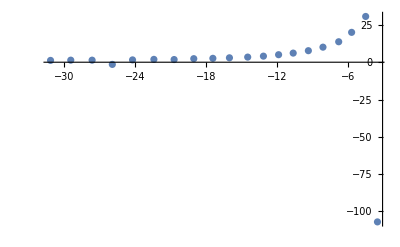

```mathematica
modelA4=a1/(δ)^2+a2/(δ)^4+θ0;
modelA2=a1/(δ)^2+θ0;
modelB4=a1/(δ-b)^2+a2/(δ-b)^4+θ0;
modelB2=a1/(δ-b)^2+θ0;
SubtractLinearSlope[data_,linearSlope_]:=Module[{detuning,angle,dataTranspose},
dataTranspose=Transpose[data];
detuning=dataTranspose[[1]];
angle=dataTranspose[[2]];
angle=angle-linearSlope*detuning;
Transpose[{detuning,angle}]
];
ZeroDataWithAsymptote[data_,nearResonanceCut_,largeDetuningCut_]:=Module[{model, dataset,nlmFit,replacements,temp,a1x,a2x,bx,θ0x,δx},
dataset=Dataset[data];
dataset=dataset[Select[Abs[#[[1]]]<largeDetuningCut&]];
dataset=dataset[Select[Abs[#[[1]]]>nearResonanceCut&]];

model=a1x/(δx)^2+a2x/(δx)^4+θ0x;
nlmFit =NonlinearModelFit[Normal[dataset],model,{{a1x,1},{a2x,1},{θ0x,0}},δx];
replacements=nlmFit["BestFitParameters"];

dataset =Transpose[Normal[data]];
dataset[[2]]=dataset[[2]]-θ0x/.replacements;
Transpose[{dataset[[1]],dataset[[2]]}]
];

negativeCutoffs={7,35};
positiveCutoffs={7,35};
detuningOffset=0;

positiveDetuningsZeroed=SubtractLinearSlope[ZeroDataWithAsymptote[positiveDetunings,positiveCutoffs[[1]],positiveCutoffs[[2]]],0-.048];

negativeDetuningsZeroed=SubtractLinearSlope[ZeroDataWithAsymptote[negativeDetunings,negativeCutoffs[[1]],negativeCutoffs[[2]]],0-.048];
allDataZeroed=Join[positiveDetuningsZeroed,negativeDetuningsZeroed];
ListPlot[negativeDetuningsZeroed,PlotRange->Full]
```

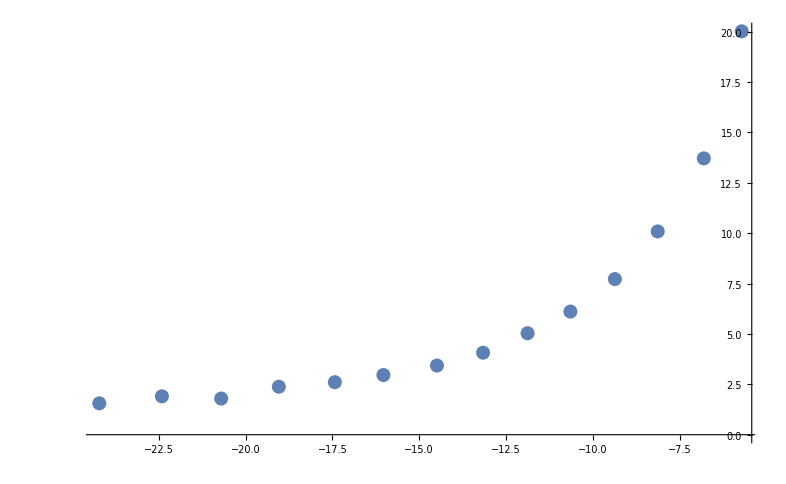

Fit Parameters for Number Density

{a1→609.275,a2→703.744,θ0→0.585981,b→1.}

Parameter Errors 1/δ^2+1/δ^4

FittedModel::constr: The property values {ParameterErrors} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

Replacements Excluding δ^4

{a1→630.116,θ0→0.505793,b→1.}

Parameter Errors 1/δ^2

FittedModel::constr: The property values {ParameterErrors} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{5.39131,0.0643027,0.}

Number Density (cm^-3):

3.77843×10^14

FittedModel::constr: The property values {ParameterErrors} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::stop: Further output of FittedModel::constr will be suppressed during this calculation.

Number Density Error (cm^-3):

1.23104×10^13

Number Density Simple(cm^-3):

3.90767×10^14

-Graphics-

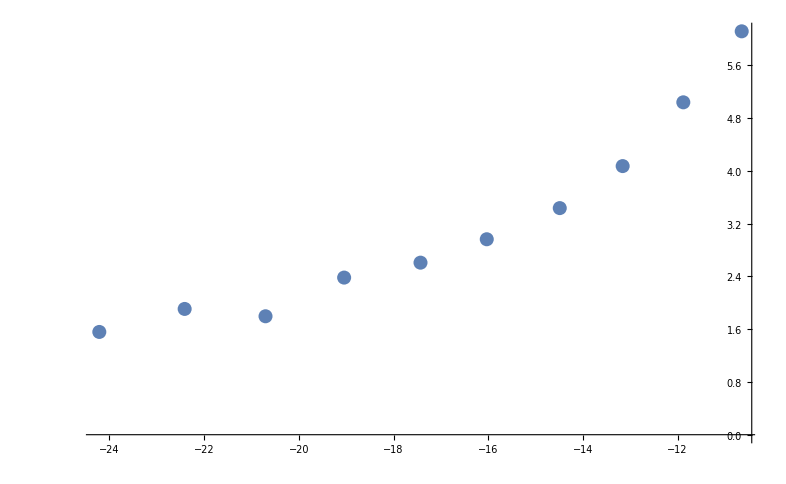

Fit Parameters for Number Density

{a1→580.494,a2→5100.81,θ0→0.606744,b→1.}

Parameter Errors 1/δ^2+1/δ^4

Replacements Excluding δ^4

{a1→632.316,θ0→0.504231,b→1.}

Parameter Errors 1/δ^2

{16.1068,0.0772212,0.}

Number Density (cm^-3):

3.59994×10^14

Number Density Error (cm^-3):

5.35214×10^13

Number Density Simple(cm^-3):

3.92131×10^14

-Graphics-

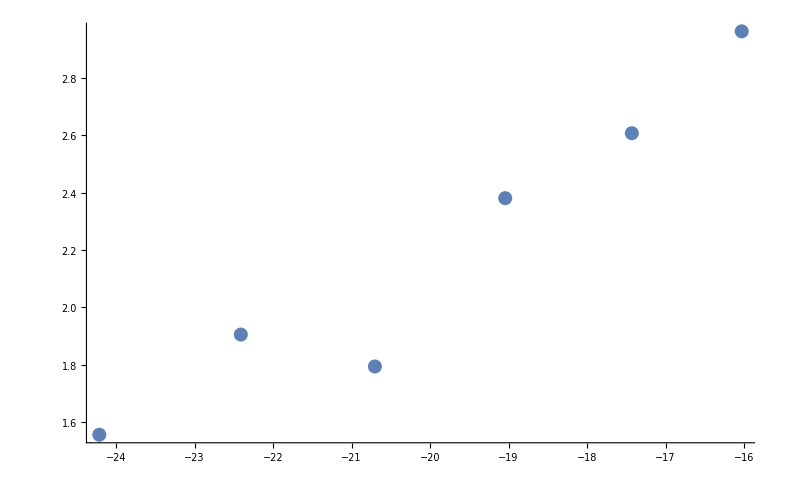

Fit Parameters for Number Density

{a1→737.893,a2→-18248.7,θ0→0.376658,b→1.}

Parameter Errors 1/δ^2+1/δ^4

Replacements Excluding δ^4

{a1→635.919,θ0→0.508489,b→1.}

Parameter Errors 1/δ^2

{84.1776,0.232795,0.}

Number Density (cm^-3):

4.57605×10^14

Number Density Error (cm^-3):

5.70267×10^14

Number Density Simple(cm^-3):

3.94366×10^14

-Graphics-

```mathematica
(* Calculates fit for data *)
(* Removes datapoints that wrapped in rotation *)
For[low=5,low<20,low+=5,
lowerBoundDetuning=low;
upperBoundDetuning= 25;
dataset=Dataset[negativeDetuningsZeroed];
dataset=dataset[Select[Abs[#[[1]]]<upperBoundDetuning&]];
dataset=dataset[Select[Abs[#[[1]]]>lowerBoundDetuning&]];
Print[ListPlot[dataset]];
alldata = Normal[dataset];
labelSize=18;

ClearAll[δ,a1,a2,c,θ0,b,nlmFit,replacements];
$Assumptions=a1>0;
$Assumptions=a2>0;
dataset=Dataset[alldata];
min=dataset[Min,2];
max=dataset[Max,2];
maxmin={max,min};
ListPlot[Normal[dataset],PlotRange->All];
νo=377.107;
Print["Fit Parameters for Number Density"];
nlmFit =NonlinearModelFit[Normal[dataset],{modelA4,a1>0},{{a1,1},{a2,1},{θ0,0},{b,1}},δ];
replacements=nlmFit["BestFitParameters"];
Print[replacements];
plot=Plot[Legended[Evaluate[model/.replacements],"A_1/(δ - B)^2+A_2/(δ - B)^4+θ_o"],{δ,30,-30},PlotRange->{Min[maxmin]-.01,Max[maxmin]+.01},PlotStyle->color,LabelStyle->labelSize];
Print["Parameter Errors 1/δ^2+1/δ^4"];
errors=nlmFit["ParameterErrors"];
{δl,θl}=Transpose[Normal[dataset]];


Print["Replacements Excluding δ^4"];
nlmFit2=NonlinearModelFit[Normal[dataset],{modelA2,a1>0},{{a1,4},{θ0,0},{b,1}},δ,AccuracyGoal->5];
replacementsNo4=nlmFit2["BestFitParameters"];
Print[replacementsNo4];
plotNo4=Plot[Legended[Evaluate[modelNo4/.replacementsNo4],"A_1/(δ - B)^2+θ_o"],{δ,30,-30},PlotRange->{Min[maxmin]-.01,Max[maxmin]+.01},PlotStyle->Red,LabelStyle->labelSize];
modelfNo4=Function[{δ},Evaluate[modelNo4/.replacementsNo4]];
{δl,θl}=Transpose[Normal[dataset]];
Print["Parameter Errors 1/δ^2"];
errorsNo4=nlmFit2["ParameterErrors"];
Print[errorsNo4];

linearRotationFit=LinearModelFit[Normal[dataset],x,x];

c=2.99792458*^8;
re=2.8179*^-15;
fge=0.34231;
k=4/3;
BdotL;
μ=9.2740*^-24;
h=6.6261*^-34;
ν0=377107.463;
conversionFactor=h/(BdotL*c*re*fge*k*μ)*10^18*10^-6;(*Conversion Factor is in 1/(Hz)^2, so we need *10^18 to convert to 1/(GHz)^2*)

Print["Number Density (cm^-3):"];
n=(a1/.replacements)* conversionFactor;
Print[n];
errors=nlmFit["ParameterErrors"];
Print["Number Density Error (cm^-3):"];
nErr=errors[[1]]*conversionFactor;
Print[nErr];

Print["Number Density Simple(cm^-3):"];
nNo4 =(a1/.replacementsNo4)*conversionFactor;
Print[nNo4];
finalResult=Show[plot,plotNo4,ListPlot[Legended[allDataZeroed,"Data Points"],LabelStyle->labelSize],Epilog->Inset[Style["1.93×10^14cm^-3",14],{20,2.5}],AxesLabel->{"Detuning\n(GHz)","Plane of Polarization (rad)"},ImageSize->Large,PlotRange->All];

Print[Rasterize[finalResult]];
fitList={{"theta_0","A_1","B","theta_0'","A_1'","B'","A_2'"},
{θ0/.replacementsNo4,a1/.replacementsNo4,b/.replacementsNo4,θ0/.replacements,a1/.replacements,b/.replacements,a1/.replacements},
{errorsNo4[[2]],errorsNo4[[1]],errorsNo4[[3]],errors[[3]],errors[[1]],errors[[4]],errors[[2]]}};
Export["fitStatistics_DetuningCutoff"<>ToString[low]<>".tsv",fitList];
Export["fitGraph_DetuningCutoff"<>ToString[low]<>".png",finalResult];
]
```